# Classification of the onset of pattern formation for the switch model in 1+1D geometry

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm.
Concentrations are measured here in μm^-3.

```mathematica
paramsSwitch={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3*4,
kdD->0.0015*4,
kdEr->1.5*4,
kdEl->10^-5*4,
kde->1,
λ->5,
μ->20};
```

## Setup

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

## Analysis

## rhoE=1900

### Adiabatic Sweep

Assume that Comsol .txt export file is saved in the same folder as this notebook.
Import adiabatic sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoE-1900.txt","List"];
```

```mathematica
adiabaticSweep[rhoE->1900]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

Determine how many data points lie within a concentration interval of 0.01 μm^-3.

```mathematica
dr=First@Differences[adiabaticSweep[rhoE->1900][[-2;;,1]]]
Round[0.01/Abs[dr]]
```

-0.00005

200

Because the pattern oscillates, the instantaneous amplitude of the pattern varies during the oscillation period. Take the maximal amplitude over a concentration interval of 0.01 μm^-3 as approximation for the maximal pattern amplitude during the oscillation.

```mathematica
patternAmplitudeSweep[rhoE->1900]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoE->1900],Round[0.01/Abs[dr]]];
```

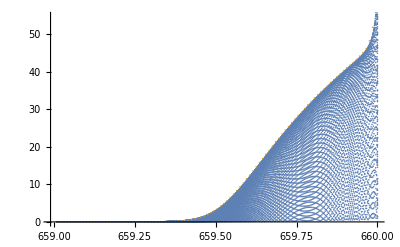

```mathematica
ListPlot[{adiabaticSweep[rhoE->1900],patternAmplitudeSweep[rhoE->1900]}]
```

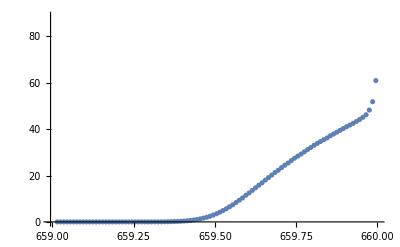

```mathematica
ListPlot[patternAmplitudeSweep[rhoE->1900]]
```

### Threshold of instability (LSA)

Boundary of instability from switchModel-1_1D-LSA-phaseDiagram.nb

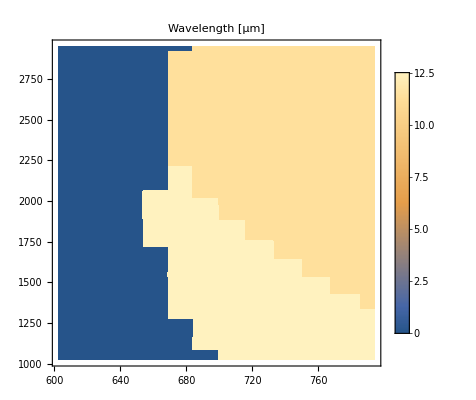

```mathematica
Monitor[sweepLSASwitchOnset[rhoE->1900]=Table[
{
rho,
testInstab[Join[{rhoD->rho/4,rhoE->1900/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[658,661,0.1]}];,rho]
```

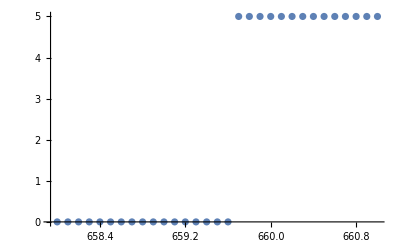

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoE->1900]]
```

659.7

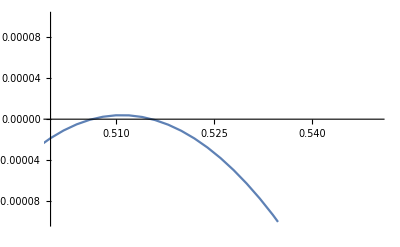

```mathematica
sweepLSASwitchOnset[[-14,1]]
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[[-14,2,2]],PlotRange->{{0.5,0.55},{-0.0001,0.0001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoE->1900]
```

{{658.,-0.000183185},{658.1,-0.000172181},{658.2,-0.000161178},{658.3,-0.000150175},{658.4,-0.000139173},{658.5,-0.000128173},{658.6,-0.000117173},{658.7,-0.000106173},{658.8,-0.0000951751},{658.9,-0.0000841776},{659.,-0.0000731809},{659.1,-0.000062185},{659.2,-0.0000511899},{659.3,-0.0000401956},{659.4,-0.0000292022},{659.5,-0.0000182096},{659.6,-7.21776×10^-6},{659.7,3.77322×10^-6},{659.8,0.0000147634},{659.9,0.0000257527},{660.,0.0000367431},{660.1,0.0000477539},{660.2,0.0000587639},{660.3,0.000069773},{660.4,0.0000807814},{660.5,0.0000917889},{660.6,0.000102796},{660.7,0.000113801},{660.8,0.000124807},{660.9,0.000135811},{661.,0.000146814}}

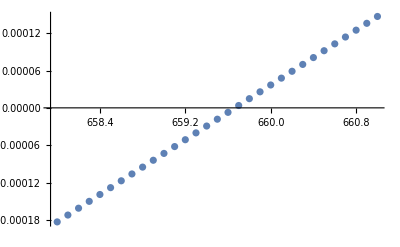

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoE->1900]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoE->1900]
```

659.666

### Simulations at fixed concentrations starting from the adiabatic sweep

#### rhoD=659.7

Assume that Comsol .txt export file is saved in the same folder as this notebook.
Import simulation at fixed concentration

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoE-1900-rhoD-659_7.txt","List"];
```

```mathematica
relaxData[rhoE->1900,rhoD->659.7]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoE->1900,rhoD->659.7]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoE->1900,rhoD->659.7]=Transpose@{times[rhoE->1900,rhoD->659.7],relaxData[rhoE->1900,rhoD->659.7]};
```

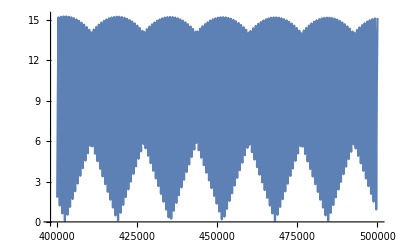

```mathematica
ListLinePlot[amplitudeRelax[rhoE->1900,rhoD->659.7]]
```

Determine maximal pattern amplitude

```mathematica
amp[rhoE->1900]={{659.7,Max[relaxData[rhoE->1900,rhoD->659.7]]}}
```

{{659.7,15.272}}

#### rhoD=659.67

Assume that Comsol .txt export file is saved in the same folder as this notebook.
Import simulation at fixed concentration

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoE-1900-rhoD-659_67.txt","List"];
```

```mathematica
relaxData[rhoE->1900,rhoD->659.67]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoE->1900,rhoD->659.67]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoE->1900,rhoD->659.67]=Transpose@{times[rhoE->1900,rhoD->659.67],relaxData[rhoE->1900,rhoD->659.67]};
```

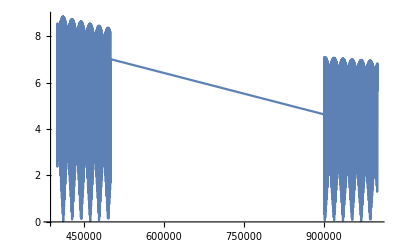

```mathematica
ListLinePlot[amplitudeRelax[rhoE->1900,rhoD->659.67]]
```

Partition data into early and late period

```mathematica
times[rhoE->1900,rhoD->659.67][[Length[times[rhoE->1900,rhoD->659.67]]/2]]
```

500000

```mathematica
amplitudeRelaxEarly=amplitudeRelax[rhoE->1900,rhoD->659.67][[;;Length[times[rhoE->1900,rhoD->659.67]]/2]];
amplitudeRelaxLate=amplitudeRelax[rhoE->1900,rhoD->659.67][[Length[times[rhoE->1900,rhoD->659.67]]/2+1;;]];
```

Determine maximal pattern amplitudes in the late period

```mathematica
peaksLate={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelaxLate,100];
```

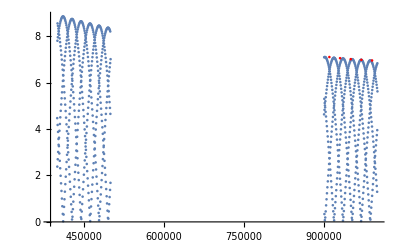

```mathematica
ListPlot[{amplitudeRelax[rhoE->1900,rhoD->659.67],peaksLate},PlotStyle->{Automatic,{Red}}]
```

Use the last peak as approximation for maximal pattern amplitude during an oscillation cycle

```mathematica
AppendTo[amp[rhoE->1900],{659.67,Min[peaksLate]}]
```

{{659.7,15.272},{659.67,6.9541}}

#### rhoD=659.65

Assume that Comsol .txt export file is saved in the same folder as this notebook.
Import simulation at fixed concentration

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoE-1900-rhoD-659_65.txt","List"];
```

```mathematica
relaxData[rhoE->1900,rhoD->659.65]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoE->1900,rhoD->659.65]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoE->1900,rhoD->659.65]=Transpose@{times[rhoE->1900,rhoD->659.65],relaxData[rhoE->1900,rhoD->659.65]};
```

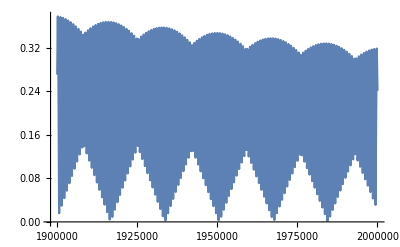

```mathematica
ListLinePlot[amplitudeRelax[rhoE->1900,rhoD->659.65]]
```

Use the last peak as approximation for maximal pattern amplitude during an oscillation cycle

```mathematica
peaks={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelax[rhoE->1900,rhoD->659.65],50];
```

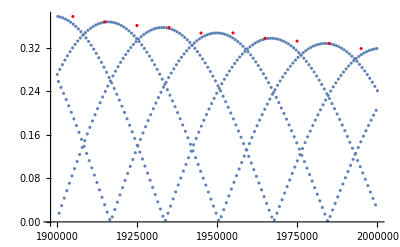

```mathematica
ListPlot[{amplitudeRelax[rhoE->1900,rhoD->659.65],peaks},PlotStyle->{Automatic,{Red}}]
```

```mathematica
AppendTo[amp[rhoE->1900],{659.65,Min[peaks]}]
```

{{659.7,15.272},{659.67,6.9541},{659.65,0.318575}}

### Result

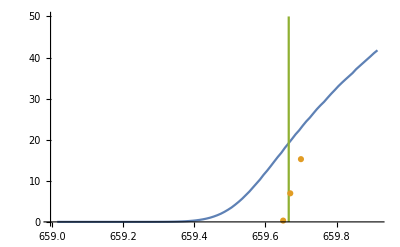

```mathematica
ListPlot[{patternAmplitudeSweep[rhoE->1900][[10;;]],amp[rhoE->1900],{{onset[rhoE->1900],0},{onset[rhoE->1900],50}}},Joined->{True,False,True}]
```

## rhoE=5000

### Adiabatic Sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoE-5000.txt","List"];
```

```mathematica
adiabaticSweep[rhoE->5000]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

```mathematica
dr=First@Differences[adiabaticSweep[rhoE->5000][[-2;;,1]]]
Round[0.01/Abs[dr]]
```

-0.0001

100

```mathematica
patternAmplitudeSweep[rhoE->5000]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoE->5000],Round[0.01/Abs[dr]]];
```

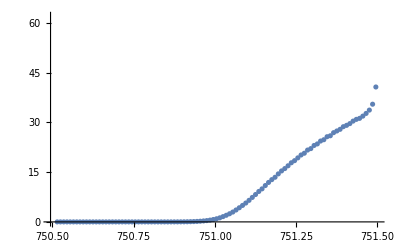

```mathematica
ListPlot[patternAmplitudeSweep[rhoE->5000]]
```

### Threshold of instability (LSA)

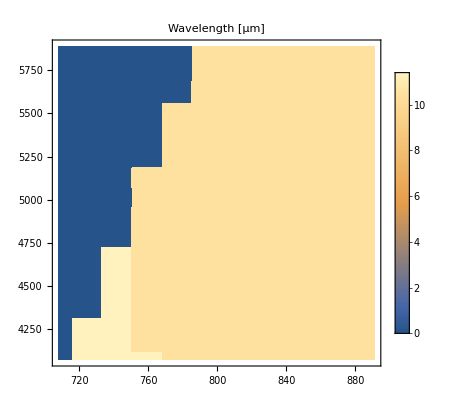

```mathematica
Monitor[sweepLSASwitchOnset[rhoE->5000]=Table[
{
rho,
testInstab[Join[{rhoD->rho/4,rhoE->5000/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[750,753,0.1]}];,rho]
```

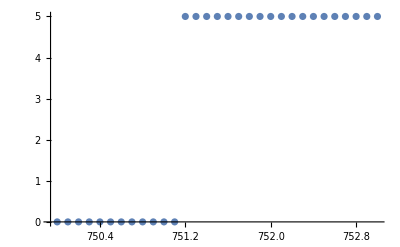

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoE->5000]]
```

```mathematica
sweepLSASwitchOnset[[13,1]]
```

751.2

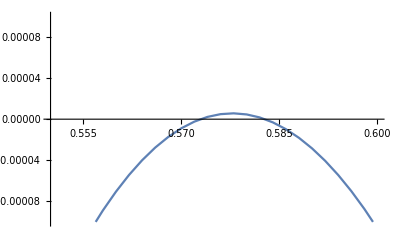

```mathematica
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[[13,2,2]],PlotRange->{{0.55,0.6},{-0.0001,0.0001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoE->5000]
```

{{750.,-0.000185458},{750.1,-0.000169526},{750.2,-0.000153593},{750.3,-0.000137662},{750.4,-0.000121731},{750.5,-0.000105801},{750.6,-0.000089871},{750.7,-0.0000739421},{750.8,-0.0000580138},{750.9,-0.0000420861},{751.,-0.0000261591},{751.1,-0.0000102328},{751.2,5.69285×10^-6},{751.3,0.0000216179},{751.4,0.0000375422},{751.5,0.0000534659},{751.6,0.000069389},{751.7,0.0000853114},{751.8,0.000101233},{751.9,0.000117154},{752.,0.000133075},{752.1,0.000148994},{752.2,0.000164914},{752.3,0.000180832},{752.4,0.00019675},{752.5,0.000212667},{752.6,0.000228584},{752.7,0.000244499},{752.8,0.000260415},{752.9,0.000276329},{753.,0.000292243}}

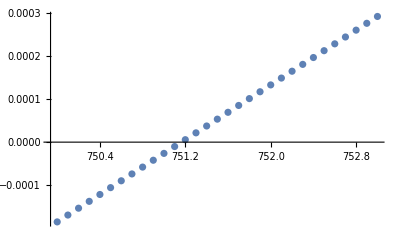

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoE->5000]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoE->5000]
```

751.164

### Long simulation starting from adiabatic sweep at fixed densities

#### rhoD=751.21

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoE-5000-rhoD-751_21.txt","List"];
```

```mathematica
relaxData[rhoE->5000,rhoD->751.21]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoE->5000,rhoD->751.21]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoE->5000,rhoD->751.21]=Transpose@{times[rhoE->5000,rhoD->751.21],relaxData[rhoE->5000,rhoD->751.21]};
```

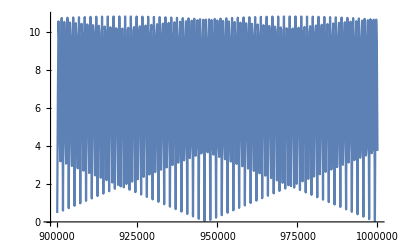

```mathematica
ListLinePlot[amplitudeRelax[rhoE->5000,rhoD->751.21]]
```

```mathematica
amp[rhoE->5000]={{751.21,Max[relaxData[rhoE->5000,rhoD->751.21]]}}
```

{{751.21,10.82}}

#### rhoD=751.15

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoE-5000-rhoD-751_15.txt","List"];
```

```mathematica
relaxData[rhoE->5000,rhoD->751.15]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoE->5000,rhoD->751.15]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoE->5000,rhoD->751.15]=Transpose@{times[rhoE->5000,rhoD->751.15],relaxData[rhoE->5000,rhoD->751.15]};
```

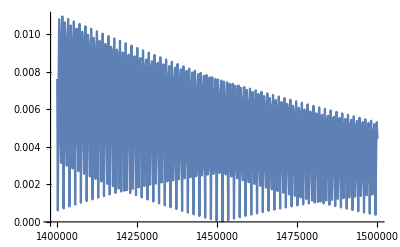

```mathematica
ListLinePlot[amplitudeRelax[rhoE->5000,rhoD->751.15]]
```

```mathematica
peaks={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelax[rhoE->5000,rhoD->751.15],10];
```

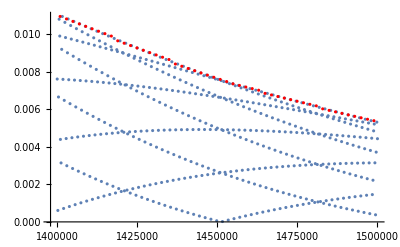

```mathematica
ListPlot[{amplitudeRelax[rhoE->5000,rhoD->751.15],peaks},PlotStyle->{Automatic,{Red}}]
```

```mathematica
AppendTo[amp[rhoE->5000],{751.15,Min@peaks}]
```

{{751.21,10.82},{751.15,0.0053978}}

### Result

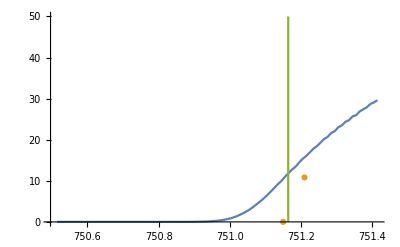

```mathematica
ListPlot[{patternAmplitudeSweep[rhoE->5000][[10;;]],amp[rhoE->5000],{{onset[rhoE->5000],0},{onset[rhoE->5000],50}}},Joined->{True,False,True}]
```

## rhoD=1000

### Adiabatic Sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoD-1000.txt","List"];
```

```mathematica
adiabaticSweep[rhoD->1000]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

```mathematica
dr=First@Differences[adiabaticSweep[rhoD->1000][[-2;;,1]]]
Round[0.01/Abs[dr]]
```

-0.0001

100

```mathematica
patternAmplitudeSweep[rhoD->1000]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoD->1000],Round[0.01/Abs[dr]]];
```

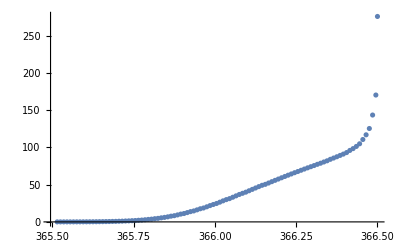

```mathematica
ListPlot[patternAmplitudeSweep[rhoD->1000]]
```

### Threshold of instability (LSA)

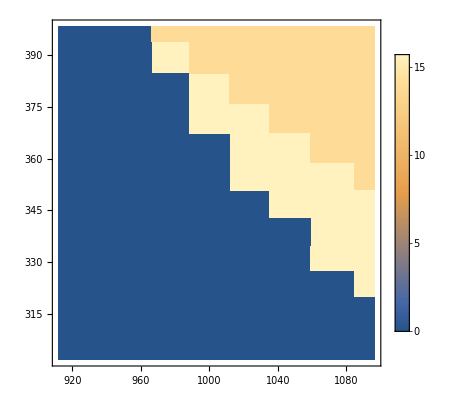

```mathematica
ListDensityPlot[{#[[1,1]],#[[1,2]],#[[2]]}&/@Select[analysisSweep,((Abs[#[[1,1]]-1000]<100)&&(Abs[#[[1,2]]-350]<50))&],InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Monitor[sweepLSASwitchOnset[rhoD->1000]=Table[
{
rho,
testInstab[Join[{rhoD->1000/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[365,368,0.1]}];,rho]
```

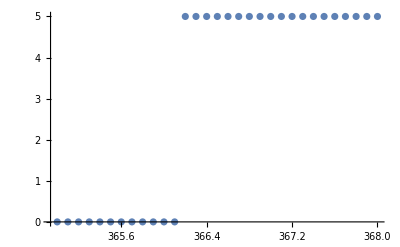

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoD->1000]]
```

```mathematica
sweepLSASwitchOnset[rhoD->1000][[13,1]]
```

366.2

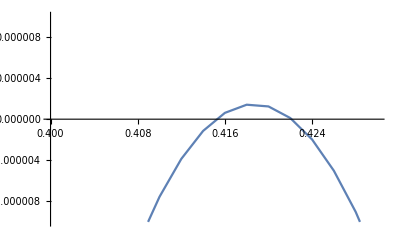

```mathematica
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[rhoD->1000][[13,2,2]],PlotRange->{{0.4,0.43},{-0.00001,0.00001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoD->1000]
```

{{365.,-0.0000424989},{365.1,-0.000038838},{365.2,-0.0000351774},{365.3,-0.0000315172},{365.4,-0.0000278573},{365.5,-0.0000241978},{365.6,-0.0000205387},{365.7,-0.0000168799},{365.8,-0.0000132215},{365.9,-9.56348×10^-6},{366.,-5.90578×10^-6},{366.1,-2.24844×10^-6},{366.2,1.40854×10^-6},{366.3,5.06516×10^-6},{366.4,8.72142×10^-6},{366.5,0.0000123773},{366.6,0.0000160329},{366.7,0.0000196881},{366.8,0.0000233429},{366.9,0.0000269974},{367.,0.0000306515},{367.1,0.0000343207},{367.2,0.0000379945},{367.3,0.0000416679},{367.4,0.0000453409},{367.5,0.0000490136},{367.6,0.0000526859},{367.7,0.0000563579},{367.8,0.0000600295},{367.9,0.0000637007},{368.,0.0000673716}}

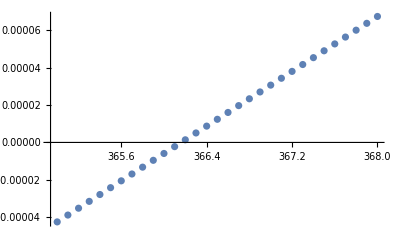

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoD->1000]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoD->1000]
```

366.161

### Long simulation starting from adiabatic sweep at fixed densities

#### rhoD=366_20

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoD-1000-rhoE-366_20.txt","List"];
```

```mathematica
relaxData[rhoD->1000,rhoE->366.2]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoD->1000,rhoE->366.2]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoD->1000,rhoE->366.2]=Transpose@{times[rhoD->1000,rhoE->366.2],relaxData[rhoD->1000,rhoE->366.2]};
```

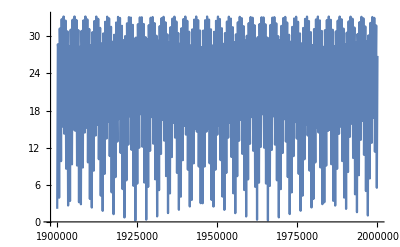

```mathematica
ListLinePlot[amplitudeRelax[rhoD->1000,rhoE->366.2]]
```

```mathematica
amp[rhoD->1000]={{366.2,Max[relaxData[rhoD->1000,rhoE->366.2]]}}
```

{{366.2,33.1969}}

#### rhoD=366.15

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoD-1000-rhoE-366_15.txt","List"];
```

```mathematica
relaxData[rhoD->1000,rhoE->366.15]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoD->1000,rhoE->366.15]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoD->1000,rhoE->366.15]=Transpose@{times[rhoD->1000,rhoE->366.15],relaxData[rhoD->1000,rhoE->366.15]};
```

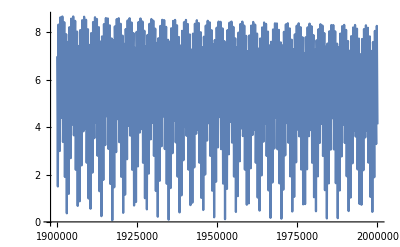

```mathematica
ListLinePlot[amplitudeRelax[rhoD->1000,rhoE->366.15]]
```

```mathematica
peaks={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelax[rhoD->1000,rhoE->366.15],50];
```

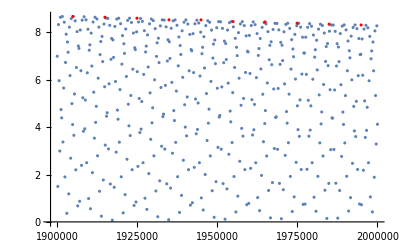

```mathematica
ListPlot[{amplitudeRelax[rhoD->1000,rhoE->366.15],peaks},PlotStyle->{Automatic,{Red}}]
```

```mathematica
AppendTo[amp[rhoD->1000],{366.15,Min@peaks}]
```

{{366.2,33.1969},{366.15,8.31469}}

### Result

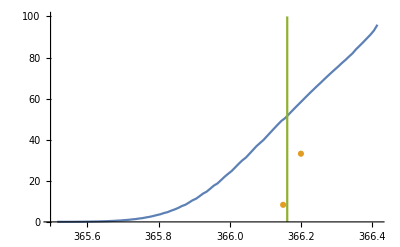

```mathematica
ListPlot[{patternAmplitudeSweep[rhoD->1000][[10;;]],amp[rhoD->1000],{{onset[rhoD->1000],0},{onset[rhoD->1000],100}}},Joined->{True,False,True}]
```

## rhoD=1900

### Adiabatic Sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoD-1900.txt","List"];
```

```mathematica
adiabaticSweep[rhoD->1900]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

```mathematica
dr=First@Differences[adiabaticSweep[rhoD->1900][[-2;;,1]]]
Round[0.01/Abs[dr]]
```

-0.0001

100

```mathematica
patternAmplitudeSweep[rhoD->1900]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoD->1900],Round[0.01/Abs[dr]]];
```

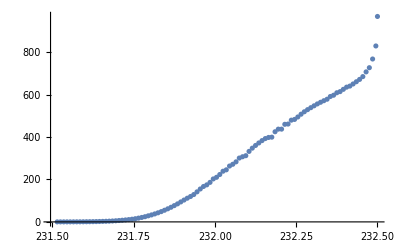

```mathematica
ListPlot[patternAmplitudeSweep[rhoD->1900]]
```

### Threshold of instability (LSA)

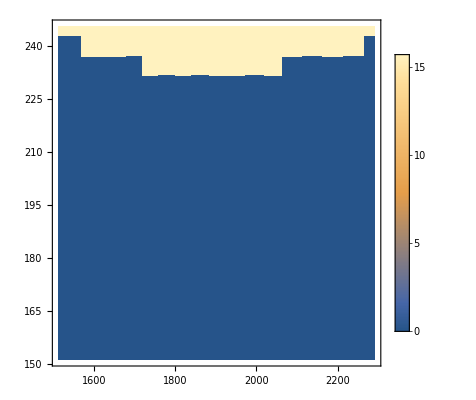

```mathematica
ListDensityPlot[{#[[1,1]],#[[1,2]],#[[2]]}&/@Select[analysisSweep,((Abs[#[[1,1]]-1900]<400)&&(Abs[#[[1,2]]-200]<50))&],InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Monitor[sweepLSASwitchOnset[rhoD->1900]=Table[
{
rho,
testInstab[Join[{rhoD->1900/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[230,233,0.1]}];,rho]
```

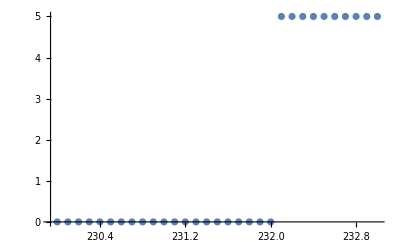

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoD->1900]]
```

```mathematica
sweepLSASwitchOnset[rhoD->1900][[22,1]]
```

232.1

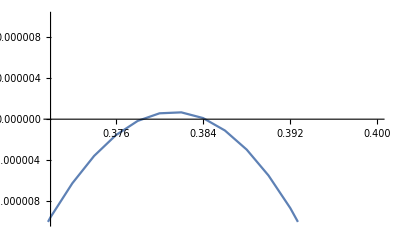

```mathematica
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[rhoD->1900][[22,2,2]],PlotRange->{{0.37,0.4},{-0.00001,0.00001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoD->1900]
```

{{230.,-0.000103579},{230.1,-0.0000986212},{230.2,-0.0000936633},{230.3,-0.0000887052},{230.4,-0.000083747},{230.5,-0.0000787885},{230.6,-0.0000738299},{230.7,-0.0000688711},{230.8,-0.0000639121},{230.9,-0.0000589529},{231.,-0.0000539935},{231.1,-0.000049034},{231.2,-0.0000440742},{231.3,-0.0000391143},{231.4,-0.0000341542},{231.5,-0.000029194},{231.6,-0.0000242335},{231.7,-0.0000192729},{231.8,-0.000014312},{231.9,-9.32883×10^-6},{232.,-4.33261×10^-6},{232.1,6.63788×10^-7},{232.2,5.66037×10^-6},{232.3,0.0000106571},{232.4,0.0000156541},{232.5,0.0000206512},{232.6,0.0000256485},{232.7,0.000030646},{232.8,0.0000356437},{232.9,0.0000406415},{233.,0.0000456396}}

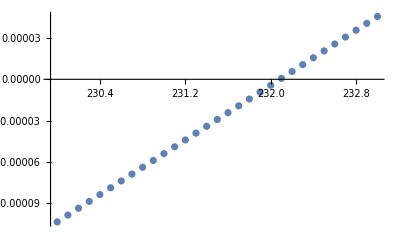

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoD->1900]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoD->1900]
```

232.087

### Long simulation starting from adiabatic sweep at fixed densities

#### rhoD=232.2

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoD-1900-rhoE-232_2.txt","List"];
```

```mathematica
relaxData[rhoD->1900,rhoE->232.2]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoD->1900,rhoE->232.2]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoD->1900,rhoE->232.2]=Transpose@{times[rhoD->1900,rhoE->232.2],relaxData[rhoD->1900,rhoE->232.2]};
```

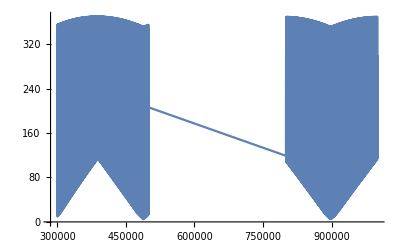

```mathematica
ListLinePlot[amplitudeRelax[rhoD->1900,rhoE->232.2]]
```

```mathematica
times[rhoD->1900,rhoE->232.2][[Length[times[rhoD->1900,rhoE->232.2]]/2]]
```

500000

```mathematica
amp[rhoD->1900]={{232.2,Max[relaxData[rhoD->1900,rhoE->232.2][[Length[times[rhoD->1900,rhoE->232.2]]/2+1;;]]]}}
```

{{232.2,369.229}}

#### rhoD=232

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoD-1900-rhoE-232.txt","List"];
```

```mathematica
relaxData[rhoD->1900,rhoE->232]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoD->1900,rhoE->232]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoD->1900,rhoE->232]=Transpose@{times[rhoD->1900,rhoE->232],relaxData[rhoD->1900,rhoE->232]};
```

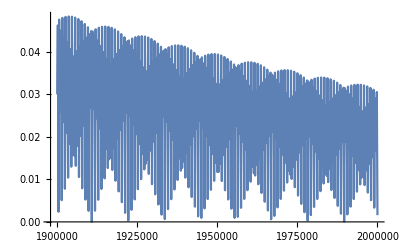

```mathematica
ListLinePlot[amplitudeRelax[rhoD->1900,rhoE->232][[Length[times[rhoD->1900,rhoE->232]]/2+1;;]]]
```

```mathematica
times[rhoD->1900,rhoE->232][[Length[times[rhoD->1900,rhoE->232]]/2]]
```

1000000

```mathematica
peaks={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelax[rhoD->1900,rhoE->232][[Length[times[rhoD->1900,rhoE->232]]/2+1;;]],50];
```

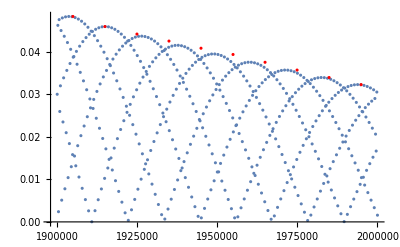

```mathematica
ListPlot[{amplitudeRelax[rhoD->1900,rhoE->232][[Length[times[rhoD->1900,rhoE->232]]/2+1;;]],peaks},PlotStyle->{Automatic,{Red}}]
```

```mathematica
AppendTo[amp[rhoD->1900],{232,Min@peaks}]
```

{{232.2,369.229},{232,0.032233}}

#### rhoD=232.08

```mathematica
relaxSweep=Import[NotebookDirectory[]<>"amplitude-rhoD-1900-rhoE-232_08.txt","List"];
```

```mathematica
relaxData[rhoD->1900,rhoE->232.08]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[relaxSweep[[-1]]][[2;;]],2][[All,2]];
```

```mathematica
times[rhoD->1900,rhoE->232.08]=Partition[ToExpression[StringReplace[StringSplit[StringTrim@#,"="][[-1]],"E"->"*10^"]]&/@Select[StringSplit[relaxSweep[[-2]]],StringContainsQ[#,"t="]&],2][[All,2]];
```

```mathematica
amplitudeRelax[rhoD->1900,rhoE->232.08]=Transpose@{times[rhoD->1900,rhoE->232.08],relaxData[rhoD->1900,rhoE->232.08]};
```

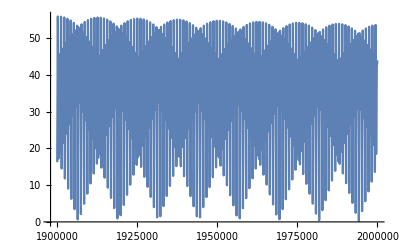

```mathematica
ListLinePlot[amplitudeRelax[rhoD->1900,rhoE->232.08]]
```

```mathematica
peaks={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[amplitudeRelax[rhoD->1900,rhoE->232.08],50];
```

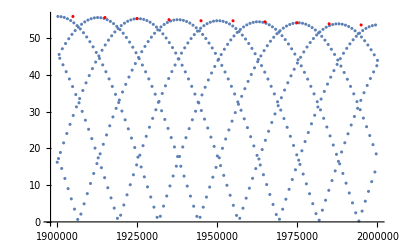

```mathematica
ListPlot[{amplitudeRelax[rhoD->1900,rhoE->232.08],peaks},PlotStyle->{Automatic,{Red}}]
```

```mathematica
AppendTo[amp[rhoD->1900],{232.08,Min@peaks}]
```

{{232.2,369.229},{232,0.032233},{232.08,53.658}}

### Result

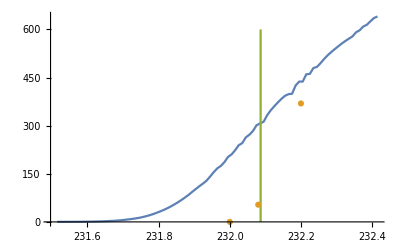

```mathematica
ListPlot[{patternAmplitudeSweep[rhoD->1900][[10;;]],amp[rhoD->1900],{{onset[rhoD->1900],0},{onset[rhoD->1900],600}}},Joined->{True,False,True}]
```

## rhoD=3000

### Adiabatic Sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoD-3000.txt","List"];
```

```mathematica
adiabaticSweep[rhoD->3000]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

```mathematica
dr=First@Differences[adiabaticSweep[rhoD->3000][[-2;;,1]]]
Round[0.1/Abs[dr]]
```

-0.001

100

```mathematica
patternAmplitudeSweep[rhoD->3000]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoD->3000],Round[0.1/Abs[dr]]];
```

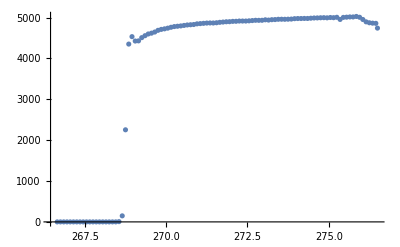

```mathematica
ListPlot[patternAmplitudeSweep[rhoD->3000]]
```

### Threshold of instability (LSA)

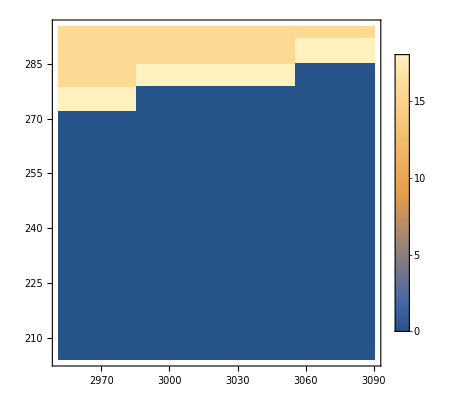

```mathematica
ListDensityPlot[{#[[1,1]],#[[1,2]],#[[2]]}&/@Select[analysisSweep,((Abs[#[[1,1]]-3000]<100)&&(Abs[#[[1,2]]-250]<50))&],InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Monitor[sweepLSASwitchOnset[rhoD->3000]=Table[
{
rho,
testInstab[Join[{rhoD->3000/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[275,278,0.1]}];,rho]
```

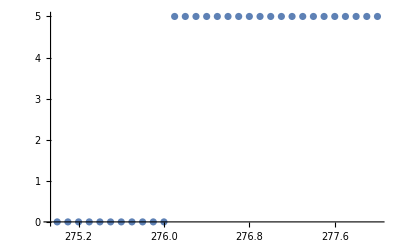

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoD->3000]]
```

```mathematica
sweepLSASwitchOnset[rhoD->3000][[12,1]]
```

276.1

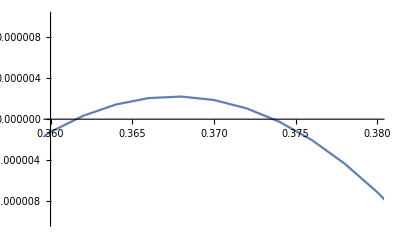

```mathematica
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[rhoD->3000][[12,2,2]],PlotRange->{{0.36,0.38},{-0.00001,0.00001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoD->3000]
```

{{275.,-0.0000382061},{275.1,-0.0000345476},{275.2,-0.0000308888},{275.3,-0.0000272298},{275.4,-0.0000235704},{275.5,-0.0000199107},{275.6,-0.0000162507},{275.7,-0.0000125625},{275.8,-8.87197×10^-6},{275.9,-5.18111×10^-6},{276.,-1.48994×10^-6},{276.1,2.20153×10^-6},{276.2,5.89329×10^-6},{276.3,9.58536×10^-6},{276.4,0.0000132777},{276.5,0.0000169704},{276.6,0.0000206634},{276.7,0.0000243567},{276.8,0.0000280502},{276.9,0.0000317441},{277.,0.0000354383},{277.1,0.0000391328},{277.2,0.0000428275},{277.3,0.000046549},{277.4,0.0000502743},{277.5,0.0000539999},{277.6,0.0000577259},{277.7,0.0000614521},{277.8,0.0000651787},{277.9,0.0000689055},{278.,0.0000726327}}

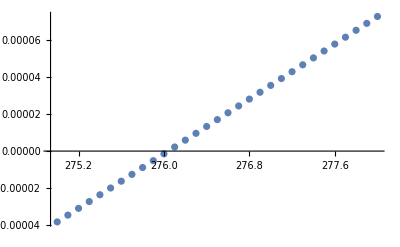

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoD->3000]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoD->3000]
```

276.04

### Result

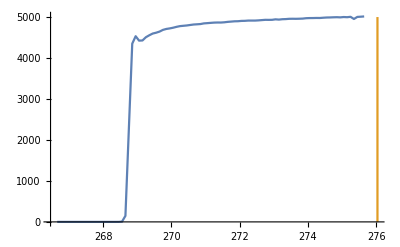

```mathematica
ListPlot[{patternAmplitudeSweep[rhoD->3000][[10;;]],{{onset[rhoD->3000],0},{onset[rhoD->3000],5000}}},Joined->{True,True}]
```

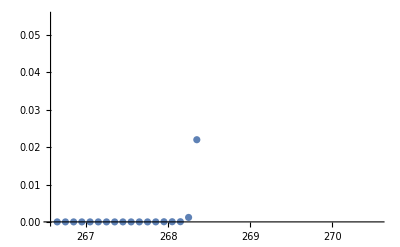

```mathematica
ListPlot[{patternAmplitudeSweep[rhoD->3000][[80;;]],{{onset[rhoD->3000],0},{onset[rhoD->3000],5000}}},Joined->{False,True}]
```

```mathematica
patternAmplitudeSweep[rhoD->3000][[80]]
```

{268.65,147.837}

## rhoD=10000

### Adiabatic Sweep

```mathematica
aSweep=Import[NotebookDirectory[]<>"amplitude-adiabaticSweep-rhoD-10000.txt","List"];
```

```mathematica
adiabaticSweep[rhoD->10000]=Partition[ToExpression[StringReplace[StringTrim@#,"E"->"*10^"]]&/@StringSplit[aSweep[[-1]]][[2;;]],2];
```

```mathematica
dr=First@Differences[adiabaticSweep[rhoD->10000][[-2;;,1]]]
Round[1/Abs[dr]]
```

-0.01

100

```mathematica
patternAmplitudeSweep[rhoD->10000]={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@Partition[adiabaticSweep[rhoD->10000],Round[1/Abs[dr]]];
```

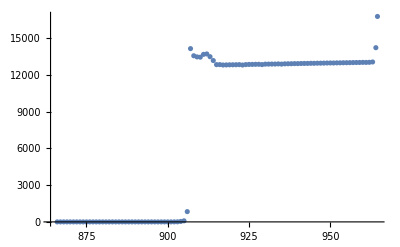

```mathematica
ListPlot[patternAmplitudeSweep[rhoD->10000]]
```

### Threshold of instability (LSA)

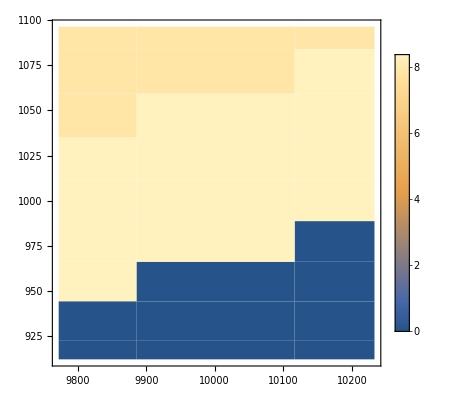

```mathematica
ListDensityPlot[{#[[1,1]],#[[1,2]],#[[2]]}&/@Select[analysisSweep,((Abs[#[[1,1]]-10000]<400)&&(Abs[#[[1,2]]-1000]<100))&],InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Monitor[sweepLSASwitchOnset[rhoD->10000]=Table[
{
rho,
testInstab[Join[{rhoD->10000/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]],"gpts"->500,"maxQ"->1]
},{rho,Range[963,966,0.1]}];,rho]
```

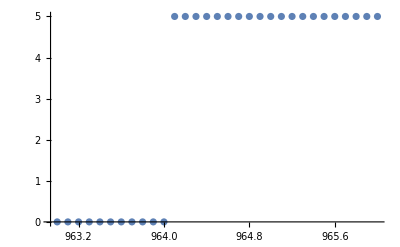

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@sweepLSASwitchOnset[rhoD->10000]]
```

```mathematica
sweepLSASwitchOnset[rhoD->10000][[12,1]]
```

964.1

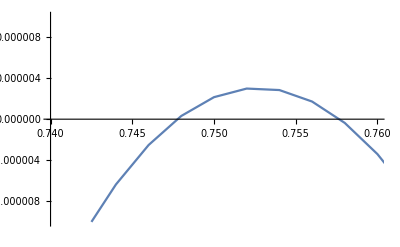

```mathematica
ListLinePlot[{#[[1]],Re@#[[2,-1]]}&/@sweepLSASwitchOnset[rhoD->10000][[12,2,2]],PlotRange->{{0.74,0.76},{-0.00001,0.00001}}]
```

```mathematica
dispMax={#[[1]],FindPeaks[Re@#[[2,2,All,2,-1]],0][[-1,-1]]}&/@sweepLSASwitchOnset[rhoD->10000]
```

{{963.,-0.0000522434},{963.1,-0.0000472231},{963.2,-0.0000422029},{963.3,-0.0000371826},{963.4,-0.0000321623},{963.5,-0.000027142},{963.6,-0.0000221217},{963.7,-0.0000171014},{963.8,-0.000012081},{963.9,-7.06064×10^-6},{964.,-2.04027×10^-6},{964.1,2.98013×10^-6},{964.2,8.00053×10^-6},{964.3,0.000013021},{964.4,0.0000180414},{964.5,0.0000230619},{964.6,0.0000280823},{964.7,0.0000331028},{964.8,0.0000381233},{964.9,0.0000431438},{965.,0.0000481644},{965.1,0.0000531849},{965.2,0.0000582055},{965.3,0.0000632261},{965.4,0.0000682467},{965.5,0.0000732673},{965.6,0.0000782879},{965.7,0.0000833086},{965.8,0.0000883333},{965.9,0.0000933628},{966.,0.0000983923}}

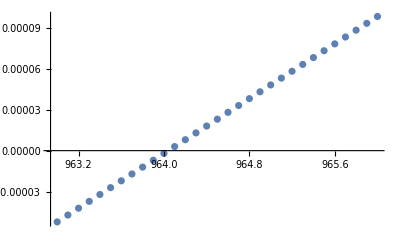

```mathematica
ListPlot[dispMax]
```

```mathematica
onset[rhoD->10000]=Block[{pos=Select[Transpose@{Range[Length@dispMax],dispMax},#[[2,2]]>0&][[1,1]],
dens=dispMax[[All,1]]},
dens[[pos-1]]+(dens[[pos]]-dens[[pos-1]])dispMax[[pos-1,2]]/(dispMax[[pos-1,2]]-dispMax[[pos,2]])];
```

```mathematica
onset[rhoD->10000]
```

964.041

### Result

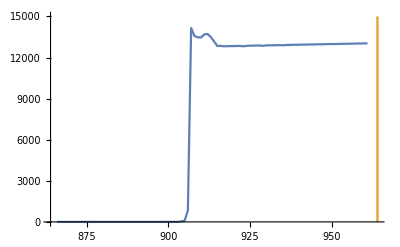

```mathematica
ListPlot[{patternAmplitudeSweep[rhoD->10000][[5;;]],{{onset[rhoD->10000],0},{onset[rhoD->10000],15000}}},Joined->{True,True}]
```